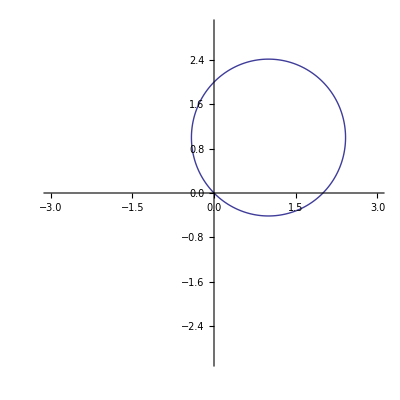

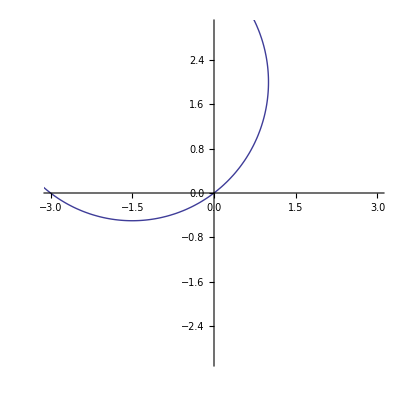

```mathematica
Clear["Global`*"];
(*Idea 2*)
(*Use Polar Cordinates*)
(*x=R*Cos[q] y=R*Sin[q]*)

(*Define the Following;
x0=; y0=;
x1=; y1=;
θ=;*)

(*Refernce To Origin*)
x1o=x1-x0;
y1o=y1-y0;

(*Equation for Radius*)
R=√(x1o^2+y1o^2);

(*Determining the polar angle of V1 at the origin*)
q=ArcTan[y1o/x1o];

(*Determing the rectangular points of V2*)
x2o=R*Cos[q+θ];
y2o=R*Sin[q+θ];

(*Offseting V2*)
x2=x2o+x0;
y2=y2o+y0;

(*Plotting*)
x0=1; y0=1;
x1=2; y1=0;
ParametricPlot[{x2,y2},{θ,0,2Pi}, PlotRange->3]

x0=-1.5; y0=2;
x1=0; y1=0;
ParametricPlot[{x2,y2},{θ,0,2Pi}, PlotRange->3]
```